```mathematica
Manipulate[Plot[{1-T+e*(2*T-1),1-T},{T,0,1}],{e,0,0.5}]
```

```mathematica
Plot[sqrt(x)+ax-z=0]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[sqrt x+ax-z=0]

```mathematica
Simplify[Sqrt[x]+a x-z==0]
```

√x+a x==z

```mathematica
Reduce[Sqrt[x]+a x-z==0,{x}]
```

Reduce::useq: The answer found by Reduce contains unsolved equation(s) {0==z-√(z^2),0==(-1+√(1+4 a z)-√2 a √(Power[«2»] Plus[«3»]))/(2 a),0==(-1-√(1+Times[«3»])-√2 a √(Power[«2»] Plus[«3»]))/(2 a)}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

(0==z-√(z^2)&&a==0&&x==z^2)||(a≠0&&0==(-1+√(1+4 a z)-√2 a √((1+2 a z-√(1+4 a z))/a^2))/(2 a)&&x==(1+2 a z-√(1+4 a z))/(2 a^2))||(a≠0&&0==(-1-√(1+4 a z)-√2 a √((1+2 a z+√(1+4 a z))/a^2))/(2 a)&&x==(1+2 a z+√(1+4 a z))/(2 a^2))

```mathematica
Reduce[x^2+a x-z==0,{x}]
```

x==1/2 (-a-√(a^2+4 z))||x==1/2 (-a+√(a^2+4 z))

```mathematica
Solve[f'''[x]x/f''[x]+1-(f''[x]+a)/f'[x]]
```

Solve::naqs: 1-(a+f''[x])/f'[x]+(x f^(3)[x])/f''[x] is not a quantified system of equations and inequalities.

Solve[1-(a+f''[x])/f'[x]+(x f^(3)[x])/f''[x]]

```mathematica
Plot[]
```

```mathematica
NormalDistribution[0,1]
```

NormalDistribution[0,1]

```mathematica
CDF[NormalDistribution[0,1],x]
```

1/2 Erfc[-x/(√2)]

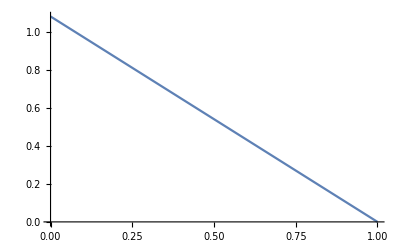

```mathematica
Plot[(1-T)*N[CDF[NormalDistribution[0,10],1]]/N[CDF[NormalDistribution[0,10],0]],{T,0,1}]
```

```mathematica
CDF[NormalDistribution[0,1],1]
```

1/2 Erfc[-1/(√2)]

```mathematica
N[1/2 Erfc[-1/(√2)]]
```

0.841345

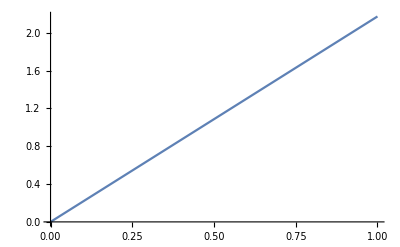

```mathematica
Plot[T/(1-N[CDF[NormalDistribution[0,10],1]]),{T,0,1}]
```

```mathematica
N[CDF[NormalDistribution[0,10],1]]
```

0.539828

```mathematica
Manipulate[Plot[{((1-T)*N[CDF[NormalDistribution[0,1],x]])/e,1-(T*(1-N[CDF[NormalDistribution[0,1],x]]))/(1-e)},{x,-10,10}],{T,0.001,1},{e,0.001,0.5}]
```

```mathematica
{{Manipulate[{Plot[{1-(T*(1-N[CDF[NormalDistribution[0,1],x]]))/(1-e)},{x,-10,2},GridLines->{{1},{1}}, GridLinesStyle->{Red,Red},PlotRange->All],Plot[{((1-T)*N[CDF[NormalDistribution[0,1],x]])/e,1},{x,-1,10}],GridLines->{{1},{1}}, GridLinesStyle->{Red,Red},PlotRange->All],{T,0,1},{e,0.0001,0.5}]}, {□}}
```

```mathematica
Transpose[{{Manipulate[{Plot[((1-T) N[CDF[NormalDistribution[0,1],x]])/e,{x,1,10}],Plot[1-(T (1-N[CDF[NormalDistribution[0,1],x]]))/(1-e),{x,-10,2}]},{T,0,1},{e,0.0001,0.5}]},{□}}]
```

{{,□}}

```mathematica
Dimensions[{{Manipulate[{Plot[((1-T) N[CDF[NormalDistribution[0,1],x]])/e,{x,1,10}],Plot[1-(T (1-N[CDF[NormalDistribution[0,1],x]]))/(1-e),{x,-10,1}]},{T,0,1},{e,0.0001,0.5}]},{□}}]
```

{2,1}

```mathematica
Flatten[{{Manipulate[{Plot[((1-T) N[CDF[NormalDistribution[0,1],x]])/e,{x,-10,1}],Plot[1-(T (1-N[CDF[NormalDistribution[0,1],y]]))/(1-e),{y,1,10}]},{T,0.001,1},{e,0.0001,0.5}]},{□}}]
```

{,□}

```mathematica
Reverse[{Manipulate[{Plot[((1-T) N[CDF[NormalDistribution[0,1],x]])/e,{x,-10,1}],Plot[1-(T (1-N[CDF[NormalDistribution[0,1],y]]))/(1-e),{y,1,10}]},{T,0.001,1},{e,0.0001,0.5}],□}]
```

{□,}

```mathematica
{{Manipulate[{Plot[{1-(T*(1-N[CDF[NormalDistribution[0,1],x]]))/(1-e)},{x,-10,2},GridLines->{{1},{1}}, GridLinesStyle->{Red,Red},PlotRange->All],Plot[{((1-T)*N[CDF[NormalDistribution[0,1],x]])/e},{x,-1,10},GridLines->{{1},{1}}, GridLinesStyle->{Red,Red},PlotRange->All]},{T,0,1},{e,0.0001,0.5}]}, {□}}
```

{{},{□}}

```mathematica
{{Manipulate[{Plot[{1-(T*(1-N[CDF[NormalDistribution[0,5],x]]))/e},{x,-10,2},GridLines->{{0.01},{0,1}}, GridLinesStyle->{Red,Red},PlotRange->All],Plot[{((1-T)*N[CDF[NormalDistribution[0,5],x]])/(1-e)},{x,-1,10},GridLines->{{0.01},{0,1}}, GridLinesStyle->{Red,Red},PlotRange->All]},{T,0,1},{e,0.0001,0.5}]}, {□}, {□}}
```

```mathematica
{{},{□},{□}}




(* Graphe pour e*)
```

```mathematica
{{Manipulate[{Plot[{(T*(1-N[CDF[NormalDistribution[0,5],x]]))/(1-N[CDF[NormalDistribution[0,5],0]])},{x,-10,2},GridLines->{{0.01},{0.5}}, GridLinesStyle->{Red,Red},PlotRange->All],Plot[{1-((1-T)*N[CDF[NormalDistribution[0,5],x]])/N[CDF[NormalDistribution[0,5],0]]},{x,-1,10},GridLines->{{0.01},{0,0.5}}, GridLinesStyle->{Red,Red},PlotRange->All]},{T,0,1}]}, {□}, {□}}
```

{{},{□},{□}}

```mathematica
{{Manipulate[{Plot[{1-(T*(1-N[CDF[NormalDistribution[0,5],x]]))/(1-N[CDF[NormalDistribution[0,5],1]])},{x,-10,2},GridLines->{{0.01},{0.5}}, GridLinesStyle->{Red,Red},PlotRange->All],Plot[{((1-T)*N[CDF[NormalDistribution[0,5],x]])/N[CDF[NormalDistribution[0,5],1]]},{x,-1,10},GridLines->{{0.01},{0,0.5}}, GridLinesStyle->{Red,Red},PlotRange->All]},{T,0,1}]}, {□}, {□}}
```

{{},{□},{□}}

```mathematica
(*Loi uniforme : le a ne modifie pas les seuils ! Seul le T est important
*){{Manipulate[{Plot[{(T*(1-(x-a)/(-2*a)))/(1-(0-a)/(-2*a))},{x,a,2},GridLines->{{0},{0.5}}, GridLinesStyle->{Red,Red},PlotRange->All],Plot[{1-(1-T)*((x-a)/(-2*a))/((0-a)/(-2*a))},{x,-1,-a},GridLines->{{0.01},{0,0.5}}, GridLinesStyle->{Red,Red},PlotRange->All]},{T,0,1},{a,-150,-10}]}, {□}, {□}}
```

{{},{□},{□}}

```mathematica
{{Manipulate[{Plot[{1-(T*(1-(x-a)/(-2*a)))/(1-(1-a)/(-2*a))},{x,a,2},GridLines->{{0},{0.5}}, GridLinesStyle->{Red,Red},PlotRange->All],Plot[{(1-T)*((x-a)/(-2*a))/((1-a)/(-2*a))},{x,-1,-a},GridLines->{{0.01},{0,0.5}}, GridLinesStyle->{Red,Red},PlotRange->All]},{T,0,1},{a,-150,-10}]}, {□}, {□}}
```

{{},{□},{□}}

```mathematica
{{Manipulate[{Plot[{N[CDF[NormalDistribution[0,10],x]],N[CDF[NormalDistribution[0,10],0]]/(1-T)},{x,0,1}],Plot[{N[CDF[NormalDistribution[0,10],x]],(N[CDF[NormalDistribution[0,10],1]]-(1-T))/T},{x,0,1}]},{T,0.001,0.999}]}, {□}, {□}}
```

{{},{□},{□}}

```mathematica
N[CDF[NormalDistribution[0,1]],0.5]
```

Erfc[(0-1. #1) 0.7] 0.5&

```mathematica
CDF[NormalDistribution[0,1],0.5]
```

```mathematica
{{Manipulate[{Plot[{(x-a)/(-2*a),-a/(-2*a*(1-T))},{x,0,1}],Plot[{1-(x-a)/(-2*a),1/T-(1-a)/(-2*a*T)},{x,0,1}]},{T,0.001,0.999},{a,-150,-10}]}, {□}, {□}}
```

{{},{□},{□}}

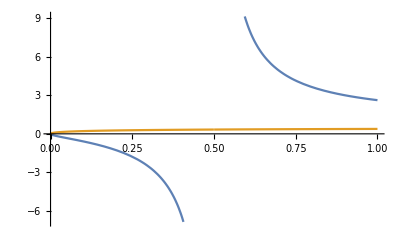

```mathematica
Manipulate[{Plot[{(3*T+Sqrt[T^2+4*T])/(2*(2T-1)),(3*T-Sqrt[T^2+4*T])/(2*(2T-1))},{T,0,1}],]
```

```mathematica
Plot[(3*T-Sqrt[T^2+4*T])/(2*(2T-1)),{T,0,1}]
```

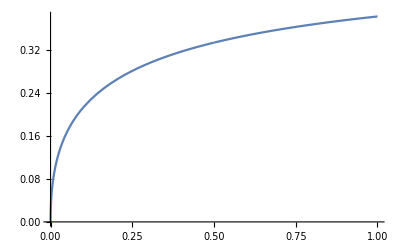

```mathematica
'
```

```mathematica
Manipulate[{Plot[{(T-3*T*x+(2*T-1)*x^2)/(1-x+e*(-1+2*x))^2, -4(0.5-e)},{e,0.01,0.49}]},{T,0.01,0.99},{x,0,1}]
```

```mathematica
Manipulate[{Plot[{(T-3*T*x+(2*T-1)*x^2)/(1-x+e*(-1+2*x))^2},{e,0.01,0.49}]},{T,0.01,0.99},{x,0,1}]
```

```mathematica
Manipulate[{Plot[{((1-e)(1-x)(1-T)-e*T*x)/((1-e)(1-x)+e*x), (0.5-e)^2,((1-e)(1-x)(1-T)-e*T*x)/((1-e)(1-x)+e*x)- (0.5-e)^2},{e,0.01,0.49}]},{T,0.01,0.99},{x,0,1}]
```

```mathematica
, Log[ Sqrt[2*Pi*Exp[1]]*sigma^2
```

```mathematica
Manipulate[Plot[{(((1-e)*Log[(1-e)]+e*Log[e]-((1-e)-(1-2e)*CDF[NormalDistribution[mu,sigma],xi])*Log[((1-e)-(1-2e)*CDF[NormalDistribution[mu,sigma],xi])]-(e+(1-2e)*CDF[NormalDistribution[mu,sigma],xi])*Log[(e+(1-2e)*CDF[NormalDistribution[mu,sigma],xi])]))/Log[2],(1-2*e)*T*CDF[NormalDistribution[mu,sigma],xi]},{xi,-1,1.5}],{e,0.01,0.49},{mu,0,1},{sigma,0.01,100},{T,0.01,0.99}]
```

```mathematica
Filling->{4->Top,1->Top,2->Top}
```

```mathematica
Assumption 1 and 2
```

```mathematica
Manipulate[Plot[{Min[1-T+T*x,x/(1-T)], Min[1-T,1-T+T*x,x/(1-T)],Legended[1-T+T*x,"C1"],Legended[x/(1-T),"C2"],x,Legended[1-T,"1-T"]},{x,0,1-T},Filling->{1->{2}},PlotRange->{{0,1},{0,1}},AxesLabel->{"F(0)","F(1)"}],{T,0.01,0.99}]
gif=Table[Plot[Min[1-T+T*x,x/(1-T)],{x,0,1}],{T,0.01,0.99}];Export["ASS.gif",gif,"DisplayDurations"->1]
```

ASS.gif

```mathematica
gif=Table[Plot[Sin[a+x],{x,0,10}],{a,0,10}];
Export["sin.gif",gif]
```

sin.gif

```mathematica
(*Export with each frame displaying for 1 second*)gif=Table[Plot[Sin[a+x],{x,0,10}],{a,0,10}];
Export["sin1second.gif",gif,"DisplayDurations"->1]
```

sin1second.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["sin1second.gif"]]]
```

```mathematica
gif=Table[Plot[{Min[1-T+T*x,x/(1-T)], Min[1-T,1-T+T*x,x/(1-T)],Legended[1-T+T*x,"C1"],Legended[x/(1-T),"C2"],x,Legended[1-T,"1-T"]},
{x,0,1-T},Filling->{1->{2}},PlotRange->{{0,1},{0,1}},AxesLabel->{"F(0)","F(1)"}],{T,0.01,0.99,.01}];Export["ASSb.gif",gif]
```

ASSb.gif

```mathematica
mp=Table[Plot[{Min[1-T+T*x,x/(1-T)], Min[1-T,1-T+T*x,x/(1-T)],Legended[1-T+T*x,"C1"],Legended[x/(1-T),"C2"],x,Legended[1-T,"1-T"]},
{x,0,1-T},Filling->{1->{2}},PlotRange->{{0,1},{0,1}},AxesLabel->{"F(0)","F(1)"}],{T,0.01,0.99,.01}];Export["ASSvideo.avi",mp]
```

ASSvideo.avi

```mathematica
SystemOpen["ASSvideo.avi"]
```

```mathematica
mpz=Table[Plot[{Min[1-T+T*x,x/(1-T)], Min[1-T,1-T+T*x,x/(1-T)],Legended[1-T+T*x,"C1"],Legended[x/(1-T),"C2"],x,Legended[1-T,"1-T"]},
{x,0,1-T},Filling->{1->{2}},PlotRange->{{0,1},{0,1}},AxesLabel->{"F(0)","F(1)"}],{T,0.01,0.99,.01}];Export["ASSDvideo.avi",mpz,"DisplayDurations"->0.2]
```

ASSDvideo.avi

```mathematica
SystemOpen["ASSDvideo.avi"]
```

```mathematica
SystemOpen["ASSBvideo.avi"]
```

```mathematica
SystemOpen["ASSavideo.avi"]
```

```mathematica
SystemOpen["ASSvideo.avi"]
```

```mathematica
Export["test.m4a",a,"BitRate"->96000]//FileByteCount
```

```mathematica
Manipulate[Plot[{(((1-e)*Log[(1-e)]+e*Log[e]-((1-e)-(1-2e)*CDF[NormalDistribution[mu,sigma],xi])*Log[((1-e)-(1-2e)*CDF[NormalDistribution[mu,sigma],xi])]-(e+(1-2e)*CDF[NormalDistribution[mu,sigma],xi])*Log[(e+(1-2e)*CDF[NormalDistribution[mu,sigma],xi])]))/Log[2],(1-2*e)*T*CDF[NormalDistribution[mu,sigma],xi]},{xi,-1,1.5}],{e,0.01,0.49},{mu,0,1},{sigma,0.01,100},{T,0.01,0.99}]
```